## Kilka drobiazgów na start z projektami

Poniżej znajduje się kilka wstępnych implementacji od których można rozpocząć projekty. Bardzo proszę to rozbudować. Można równiez stosować zupełnie inne podejścia.

## Równanie falowe, równanie Schroedingera, równanie Poissona

Załóżmy, że mamy do rozwiązania równanie falowe w postaci (zakładamy, że prędkość rozchodzenia się fali wynosi 1):

(∂^2 u)/(∂t^2)(t; x , y) = (∂^2/(∂x^2) + ∂^2/(∂y^2))u(t; x , y) = ∇^2 u(t; x ,y)

Chcemy wykorzystać do tego komputer dlatego zakładamy, że wartość amplitudy znamy na węzłach siatki oddalonych o δ:

u_ij= u(t; i δ , j δ)

Jeżeli wartość δ jest niewielka to dobrym przybliżeniem Laplacianu może być wyrażenie:

∇^2 u(t; i δ , jδ) ≈1/δ^2 (u_((i + 1)j) +u_((i - 1)j) + u_(i (j + 1))+u_(i(j - 1)) - 4 u_ij)

Jeżeli dodatkowo wszystkie u_ijułożone są w tabelkę:

(u_11 | u_12 | ...
u_21 | u_22 | ...
... | ... | ...)

to wartości ∇^2 u na tej siatce:

(∇^2 u(t; 1 δ , 1δ)  | ∇^2 u(t; 1 δ , 2δ)  | ...
∇^2 u(t; 2 δ , 1δ)  | ∇^2 u(t; 2 δ , 2δ)  | ...
... | ... | ...)≈konwolucja 1/δ(0 | 1 | 0
1 | -4 | 0
0 | 1 | 0) z macierzą (u_11 | u_12 | ...
u_21 | u_22 | ...
... | ... | ...)

W Mathematice możemy skorzystać z ListConvolve. Najpierw tworzymy jądro konwolucji:

```mathematica
δ = 0.1;
lpl = {
{0.0 , 1.0 , 0.0},
{1.0 , -4.0 , 1.0},
{0.0 , 1.0 , 0.0}
}/δ^2;
```

Teraz tworzymy wstępną tabelkę zawierającą amplitudy fali  .... 

.... może, żeby nie było zbyt łatwo nie będziemy tutaj rozwiązywać równania falowego ani równania Schroedingera tylko równanie przewodnictwa cieplnego ( https://en.wikipedia.org/wiki/Heat_equation ):

(∂u)/(∂t)u(t; x , y)  = ∇^2 u(t; x ,y)

gdzie u(t; x , y) jest temperaturą na płaszczyźnie w pewnym miejscu. Stworzymy tabelkę temperatur w chwili t = 0:

```mathematica
u0 = Table[If[(i - 20)^2 + (j - 20)^2 < 10^2 , 1.0 , 0.0] , {i , 0 , 99} , {j , 0 , 99}];
ArrayPlot[u0 , PlotLegends->Automatic]
```

-Graphics-

Aby uzyskać rozkład temperatur w kolejnych chwilach czasowych można zastosować prostą metodę Eulera ( https://en.wikipedia.org/wiki/Euler_method ):

```mathematica
iter[dt_][u_]:= u + dt ListConvolve[lpl , u , {2 , 2}];
history[n_]:=NestList[iter[0.0001] , u0 , n];
```

Proszę zauważyć, że NestList załatwia nam periodyczne granice.

```mathematica
hist = history[20000];
```

```mathematica
Manipulate[ArrayPlot[
hist[[i]],
PlotLegends->Automatic
] , {i , 1 , Length[hist] , 1}]
```

Aby rozwiązać równanie falowe można zastosować Algorytm skokowy ( https://en.wikipedia.org/wiki/Leapfrog_integration ). 

Dla równania Schroedingera, powinna wystarczyć metoda Eulera ( https://en.wikipedia.org/wiki/Euler_method ). Równanie, przynajmniej prawa strona równania bardzo przypomina rónanie cieplne oraz równanie falowe gdy założymy, że wszędzie potencjał jest 0 i mamy jedynie energię kinetyczną. Aby nie było zbyt nudno, załóżmy, że w niektórych miejscach potencjał jest ∞ (można na przykład zamknąć czątkę w pudle z dwoma dziurkami, potencjał na ścianach pudła jest ∞). Nie musimy tutaj zmieniać równania i metody, wystarczy po każdym kroku czasowym w odpowiednich miejscach zerować funkcję falową. Można na przykład pomnożyć element po elemencie tabelkę:
(u_11 | u_12 | ...
u_21 | u_22 | ...
... | ... | ...)
zawierającą wartości funkcji falowej przez tabelkę zawierającą 0.0 lub 1.0. 
(0.0 | 1.0 | ...
1.0 | 1.0 | ...
... | ... | ...)

Dla równania Poissona można wykorzystać Metodę Jacobbiego ( można poczytać na przykład tutaj http://physics.ujep.cz/~dkramolis/plazma/Dalsi%20materialy/Poisson_1D_2.pdf ). Można również skorzystać z ListConvolve trzeba jednak zmodyfikować jądro. Załóżmy dodatkowo, że po każdej iteracji potencjał na określonych węzłach jest zawsze zmieniony do potencjału elektrody obejmującej dane węzły. 

Równania rozwiązujemy z wykorzystaniem periodycznych warunków brzegowych. Czy jest lepsza metoda wizualizacji danych biorąca to pod uwagę, na przykład na torusie?

## Liczenie pi

Rozmawialiśmy o tym na zajęciach. Na wszelki wypadek, kilka równań (m1, m2 to masy klocków, v1 , v2 to prędkości klocków, t to czas):

```mathematica
Solve[1/2 m1 v1^2 + 1/2 m2 v2^2 ==1/2 m1 v1p^2 + 1/2 m2 v2p^2&&m1 v1 + m2 v2 ==m1 v1p + m2 v2p  , {v1p  , v2p}]//FullSimplify
```

{{v1p→v1,v2p→v2},{v1p→(m1 v1-m2 v1+2 m2 v2)/(m1+m2),v2p→(2 m1 v1-m1 v2+m2 v2)/(m1+m2)}}

```mathematica
Solve[x1 + v1 t == 0 ,t]
```

{{t→-x1/v1}}

```mathematica
Solve[x1 +v1 t +d1== x2 + v2 t  , t]
```

{{t→(-d1-x1+x2)/(v1-v2)}}

Dodatkowo proszę przyjrzeć się funckji Sound oraz SampledSoundList jeżeli do animacji chcemy dodać dźwięk.

## Symulacje układów planetarnych

Bardzo prosiłbym w pierwszym kroku znaleźć warunki początkowe dla planet z układu słonecznego. Następnie wystarczy te warunki wykorzystać w rozwiązaniu numerycznym równań Newtona. Poniżej jest przykład z dwoma planetami. Zakładamy, że masy oraz stała grawitacji wynoszą 1:

```mathematica
{x1fun , y1fun , x2fun , y2fun} = NDSolveValue[
{
x1''[t] == (x2[t] - x1[t])/(((x2[t] - x1[t])^2+(y2[t] - y1[t])^2)^(3/2)),
y1''[t] == (y2[t] - y1[t])/(((x2[t] - x1[t])^2+(y2[t] - y1[t])^2)^(3/2)),
x2''[t] == (x1[t] - x2[t])/(((x2[t] - x1[t])^2+(y2[t] - y1[t])^2)^(3/2)),
y2''[t] == (y1[t] - y2[t])/(((x2[t] - x1[t])^2+(y2[t] - y1[t])^2)^(3/2)),
x1[0] == -1.0,
y1[0] == 0.0,
x2[0] == 1.0,
y2[0] == 0.0,
x1'[0] == 0.0,
y1'[0] == 0.2,
x2'[0] == 0.0,
y2'[0] == -0.2
},
{x1 , y1 , x2 , y2} ,{t , 0 , 20}];
```

```mathematica
Manipulate[Graphics[{PointSize[Large],{Red , Point[{x1fun[t] , y1fun[t]}]} , {Blue , Point[{x2fun[t] , y2fun[t]}]}} , PlotRange->{{-2 , 2} , {-2 , 2}}] , {t , 0 , 20}]
```

Powyżej jest przykład ze zmyslonymi warunkami początkowymi oraz nierealistyczną stałą grawitacji oraz masami. Wszystko dzieje się w dwóch wymiarach. Proszę sprawić aby symulacja była bardziej realistyczna, w trzech wymiarach, a wizualizacja bardziej dokładna.

## Makaronowy most

Most można reprezentować dwoma listami, pierwsza zawiera współrzędne węzłów:
   {{x1 , y1} , {x2 , y2} , ...}
Druga zawiera indeksy węzłów połączonych nitka makaronu, na przykład łączymy węzeł 1 oraz 2, węzeł 2 oraz 3:
   {{1 , 2} , {2 , 3} , ...}
Poniżej znajduje się funkcja, którą można wykorzystać do rysowania mostu:

```mathematica
draw[nodes_ , connections_]:=Graphics[{{PointSize[Large] , Point/@nodes},{Blue , MapIndexed[Function[{x ,i} , Text[Style[ToString[i[[1]]] , FontSize->Large],x,{-1 , -1}]] , nodes]} , {Function[lne , Line[{nodes[[lne[[1]]]] , nodes[[lne[[2]]]]}]]/@connections}}];
```

```mathematica
nodes = {{-1.0 , 0.0} , {1.0 , 0.0} , {0.0 , -1.0} , {0.0 , 1.0}};
connections = {{1 , 2} , {2 , 3} , {3 , 1} , {1 , 4} , {2 , 4}};
```

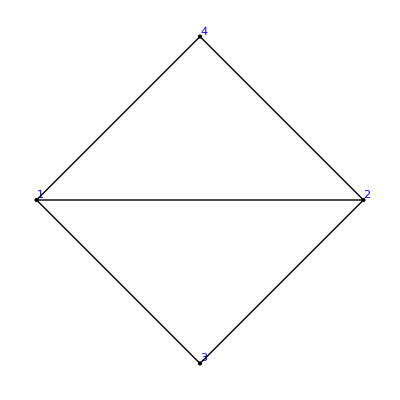

```mathematica
draw[nodes , connections]
```

Dla każdego węzła musimy ułożyć odpowiednie równania. Zakładamy, że węzły nie ruszają się, nawet jeżeli do jednego z nich przyłozymy siłę. Aby ułozyć te równania trzeba znać pozycje sąsiednich węzłów. Na przykład dla węzła 2 mamy sąsiednie węzły 3 oraz 4:

```mathematica
Cases[connections , {2 , i_}:>i]
```

{3,4}

Pozycja węzła 2 to:

```mathematica
nodes[[2]]
```

{1.,0.}

natomiast pozycja sąsiadów:

```mathematica
Cases[connections , {2 , i_}:>nodes[[i]]]
```

{{0.,-1.},{0.,1.}}

## Układy optyczne

Na początek pojedyncza powierzchnia soczewki. c1 oraz c2 to prędkość światła przed oraz za powierzchnią. f to funkcja, f[t] to funkcja zwracająca punkt na powierzchni, t = 0 ... 1:

```mathematica
dt = 0.1;
makeSurface[c1_ , c2_ , f_]:={c1 , c2 ,Table[f[t] ,{t , 0 , 1 ,dt}]};
```

Dla przykładu weźmiemy kawałek okręgu:

```mathematica
sphere[t_]:= {-Cos[π/2 (2.0 t - 1.0)] , Sin[π/2 (2.0 t - 1.0)]};
```

```mathematica
surface = makeSurface[1 , 1.1 , sphere];
```

Powierzchnię można naryskować:

```mathematica
drawSurface[{c1_ , c2_ , lst_}]:=Graphics[{Point/@lst , Line[lst]}];
```

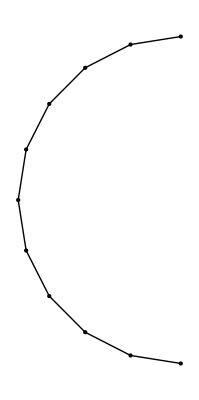

```mathematica
drawSurface[surface]
```

Teraz można znaleźć segment z którym przecina się promień startujący z pozycji:
   {-2 , 2}
oraz mający kierunek:
   {1 , 0.2}

```mathematica
ray = {{-2 , 0} , {1 , 0.2}};
```

```mathematica
Show[drawSurface[surface] , Graphics[HalfLine@@ray] , Axes->{True,False}]
```

-Graphics-

Funkcja intersection zwraza 0.0 jeżeli przecięcie z ray następiło zaraz na początku odcinka rozpoczynającego się w punkcie
   {segmentStart1 , segmentStart2}
oraz kończącego się w punkcie:
   {segmentEnd1 , segmentEnd2}.
Jeżeli przecięcie nastąpiło pod koniec tego odcinka to intersection zwróci 1.0. Można tą wunkcję również wykorzystać do sprawdzenie, czy przecięcie z danym odcinkiem następiło. Jeżeli dostaniemu wartość intersection mniejszą od 0.0 lub większą od 1.0 oznacza to, że nie nastąpiło przecięcie z odcinkiem.

```mathematica
intersection[{{{rayStart1_ , rayStart2_} , {rayDirection1_ , rayDirection2_}} , {{segmentStart1_ , segmentStart2_} , {segmentEnd1_ , segmentEnd2_}}}]:=(-((-rayDirection2 rayStart1+rayDirection1 rayStart2+rayDirection2 segmentStart1-rayDirection1 segmentStart2)/(rayDirection2 segmentEnd1-rayDirection1 segmentEnd2-rayDirection2 segmentStart1+rayDirection1 segmentStart2)));
```

Definicja funkcji intersection jest powiązana z równaniem poniżej. Prosze się zastanowić nad tym skąd się biorą:

```mathematica
Solve[Thread[{rayStart1 , rayStart2} + t1 {rayDirection1 , rayDirection2} == {segmentStart1 , segmentStart2} + t2 {(segmentEnd1 - segmentStart1) , (segmentEnd2 - segmentStart2)}] , {t1 , t2}]
```

{{t1→-(rayStart2 segmentEnd1-rayStart1 segmentEnd2-rayStart2 segmentStart1+segmentEnd2 segmentStart1+rayStart1 segmentStart2-segmentEnd1 segmentStart2)/(rayDirection2 segmentEnd1-rayDirection1 segmentEnd2-rayDirection2 segmentStart1+rayDirection1 segmentStart2),t2→-(-rayDirection2 rayStart1+rayDirection1 rayStart2+rayDirection2 segmentStart1-rayDirection1 segmentStart2)/(rayDirection2 segmentEnd1-rayDirection1 segmentEnd2-rayDirection2 segmentStart1+rayDirection1 segmentStart2)}}

Najpierw układamy argumenty dla intersection. Proszę rozebrać to wyrażenie na kawałki aby zrozumieć jak funkcjonuje:

```mathematica
argumentsForIntersection = Function[x , {ray , x}]/@Partition[(Riffle[RotateLeft[surface[[3]]] , surface[[3]]]) , 2][[1;;-2]];
```

Teraz mapujemy funkcję intersection:

```mathematica
inter = intersection/@argumentsForIntersection
```

{-11.6414,-5.51819,-3.1113,-1.68895,-0.627341,0.331614,1.39634,2.97524,7.10267,-46.6566}

Sprawdzamy z którym odcinkiem jest przecięcie:

```mathematica
Position[inter , x_/;x>=0&&x<1]
```

{{6}}

```mathematica
Show[drawSurface[surface] , Graphics[HalfLine@@ray], Graphics[{Thick , Red , Line[{surface[[3 , 6]] , surface[[3,7]]}]}] , Axes->{True,False}]
```

-Graphics-

Następnie należy to trochę zautomatyzować. Potem sworzyć na przykład funkcję:
   iterateRay[ray , surface] 
 zwracającą nowy promień po przejściu przez powierzchnię. Potem można rozbudować.

## Szereg Fouriera

Proszę przyjrzeć się : https://mathworld.wolfram.com/FourierSeries.html . Będziemy starali się korzystając z wzoru (20) przybliżyć kształt opisany liniami pomiędzy punktami w pts:

```mathematica
pts = {{-1.0 , -1.0} , {1.0 , -1.0} , {1.0 , 1.0} , {-1.0 , 1.0} , {0.0 , 0.0}};
```

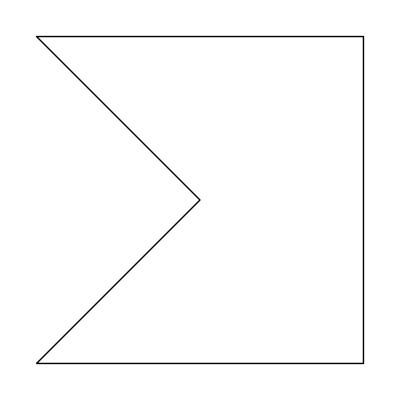

```mathematica
shape = Graphics[Line[Join[pts , {pts[[1]]}]]]
```

Najpierw potrzebna będzie funkcja akceptująca liczbę 0 ... 1 i zwracająca punkt na tej figurze. Proszę się przyjrzeć propozycji:

```mathematica
point[t_]:=
(1.0 - Length[pts]Mod[t , 1.0/Length[pts]])pts[[1 + Floor[t Length[pts]]]] + 
(Length[pts]Mod[t , 1.0/Length[pts]]) RotateLeft[pts][[1 + Floor[t Length[pts]]]];
```

Można sprawdzić czy to działa ale jest problem w okolicach 1 dlatego najpierw definiujemy almostOne:

```mathematica
almostOne = 0.99999;
```

zachęcam do znalezienia lepszego rozwiązania. 

Poniżej znajduje się punkt wyliczony z wykorzystaniem point dla różnych wartości t.

```mathematica
Manipulate[Show[Graphics[{PointSize[Large] , Point[point[almostOne t]]}],shape] , {t , 0.0 , 1.0}]
```

Patrząc na (20) oraz (26) z https://mathworld.wolfram.com/FourierSeries.html będziemy potrzebowali nieco innej funkcji. Tym razem argumenty są od -π do π i zwracana jest liczba zespolona. Część rzeczywista to np x a część urojona to y:

```mathematica
complexPoint[t_?NumericQ]:= Complex@@point[(t/π + 1.0)/2.0];
```

Zgodnie ze wzorem (26) teraz wystarczy wycałkować. Ograniczymy się do n = -m ... m:

```mathematica
m = 4;
```

```mathematica
aPts = Monitor[
Table[
{n,1/(2 π)Quiet[NIntegrate[complexPoint[almostOne x] Exp[-ⅈ n x] , {x , -π , π}]]} , {n , -m , m}
] , {n}];
```

aPts zawiera współczynniki A_n . Quiet jest dodane aby wyciszyć błędy dotyczące zbieżności całek. Zachęcam do znalezienia lepszego rozwiązania. 

Teraz wystarczy postawić do (20). epiVal zwraca przybliżone współrzędne punktów leżących na figurze z wykorzystaniem epicykli:

```mathematica
epiVal[aPoints_][x_]:=ReIm[Total[#[[2]] Exp[ⅈ #[[1]]x]&/@aPoints]]
```

```mathematica
Manipulate[Show[Graphics[{PointSize[Large] , Point[epiVal[aPts][t]]}],shape , PlotRange->{{-2 , 2} , {-2 , 2}}] , {t , -π , π}]
```

Widać, że punkt podąża za kształtem, ale niezbyt idealnie. Można spróbować to rozwinąć - może w stylu https://youtu.be/qS4H6PEcCCA?si=w1g0GoOtoGIvHYDK .